```mathematica
n=7
b=2
a=-2
h=(b-a)/n
XDT={};YDT={};
For[i=0,i≤n,i++,
xdata[i]=a+i×h;
ydata[i]=N[Exp[-xdata[i]]+0.1*(-1)^(i+2)];
XDT=Append[XDT,xdata[i]];
YDT=Append[YDT,ydata[i]];];
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-10/7}, {-6/7}, {-2/7}, {2/7}, {6/7}, {10/7}, {2}}) ({{7.48905609893065}, {4.072733883598096}, {2.4564184423836606}, {1.2307121974473498}, {0.851477293075286}, {0.32437284567695}, {0.3396510364417758}, {0.0353352832366127}})
Array[difftab,{n+1,n+1},{0,0}];
For[k=1,k≤n,k++,
For[i=n,i≥n-k,i--,difftab[i,k]=""]];
For[i=0,i≤n,i++,difftab[i,0]=ydata[i]];
For [k=1, k≤n,k++,
For[i=0,i≤n-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata[i+k]-xdata[i])]];
tab1 = Array[difftab,{n+1,n+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

{-14.9781,-5.81819,-2.1055,-0.351632,0.243279,0.278034,0.485216,0.0706706}

7.48906 | -5.97856 |  2.75626 | -1.25892 |  0.72892 | -0.45347 |  0.25732 | -0.12788
 4.07273 | -2.82855 |  0.59812 |  0.40719 | -0.56672 |  0.42876 | -0.25418 | 
 2.45642 | -2.14499 |  1.29616 | -0.88817 |  0.65832 | -0.44272 |  | 
 1.23071 | -0.66366 | -0.22643 |  0.61655 | -0.60659 |  |  | 
 0.85148 | -0.92243 |  0.83052 | -0.76994 |  |  |  | 
 0.32437 |  0.02674 | -0.48938 |  |  |  |  | 
 0.33965 | -0.53255 |  |  |  |  |  | 
 0.03534 |  |  |  |  |  |  |

```mathematica
pln = difftab[0,0]+difftab[0,1]×(x-xdata[0]);
n=7;lst=List[pln];
For[k=2,k≤n,k++,
pln=lst[[k-1]]+difftab[0,k]×∏_(i=0)^(k-1) (x-xdata[i]);
lst=Append[lst,pln]];
nwtn[x_]:=N[lst[[n]]];
ColumnForm[lst]
```

7.48906-5.97856 (2+x)
7.48906-5.97856 (2+x)+2.75626 (10/7+x) (2+x)
7.48906-5.97856 (2+x)+2.75626 (10/7+x) (2+x)-1.25892 (6/7+x) (10/7+x) (2+x)
7.48906-5.97856 (2+x)+2.75626 (10/7+x) (2+x)-1.25892 (6/7+x) (10/7+x) (2+x)+0.728921 (2/7+x) (6/7+x) (10/7+x) (2+x)
7.48906-5.97856 (2+x)+2.75626 (10/7+x) (2+x)-1.25892 (6/7+x) (10/7+x) (2+x)+0.728921 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.453475 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.48906-5.97856 (2+x)+2.75626 (10/7+x) (2+x)-1.25892 (6/7+x) (10/7+x) (2+x)+0.728921 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.453475 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.25732 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.48906-5.97856 (2+x)+2.75626 (10/7+x) (2+x)-1.25892 (6/7+x) (10/7+x) (2+x)+0.728921 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.453475 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.25732 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)-0.127876 (-10/7+x) (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)

```mathematica
ColumnForm[Collect[lst,x]]
```

-4.46807-5.97856 x
3.40696+3.47147 x+2.75626 x^2
0.323901-3.8251 x-2.63909 x^2-1.25892 x^3
0.833933-0.83291 x+2.47823 x^2+2.07329 x^3+0.728921 x^4
0.92459-0.618354 x+1.52633 x^2-0.517991 x^3-1.21454 x^4-0.453475 x^5
0.968683-0.565442 x+0.941601 x^2-1.23819 x^3-0.689401 x^4+0.428764 x^5+0.25732 x^6
0.999987-0.54979 x+0.500188 x^2-1.45889 x^3+0.0413166 x^4+0.794123 x^5+0.00156861 x^6-0.127876 x^7

```mathematica
data = {{-2,7.48905609893065},{-10/7,4.072733883598096},{-6/7,2.4564184423836606},{-2/7,1.2307121974473498},{2/7,0.851477293075286},{6/7,0.32437284567695},{10/7,0.3396510364417758},{2,0.0353352832366127}}
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]
```

{{-2,7.48906},{-10/7,4.07273},{-6/7,2.45642},{-2/7,1.23071},{2/7,0.851477},{6/7,0.324373},{10/7,0.339651},{2,0.0353353}}

0.999987-0.54979 x+0.500188 x^2-1.45889 x^3+0.0413166 x^4+0.794123 x^5+0.00156861 x^6-0.127876 x^7

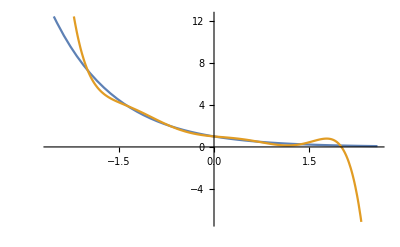

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-h,b+h}]
```

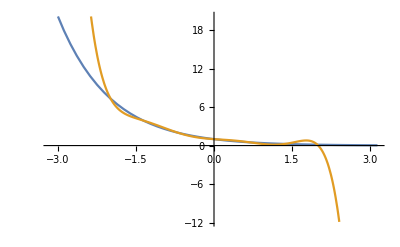

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-2h,b+2h}]
```

```mathematica
Pln={};P[n+1]=0;
For[i=n,i≥0,i--,P[i]=difftab[0,i]+(x-xdata[i])P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln]
```

-0.127876
0.25732-0.127876 (-10/7+x)
-0.453475+(0.25732-0.127876 (-10/7+x)) (-6/7+x)
0.728921+(-0.453475+(0.25732-0.127876 (-10/7+x)) (-6/7+x)) (-2/7+x)
-1.25892+(0.728921+(-0.453475+(0.25732-0.127876 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)
2.75626+(6/7+x) (-1.25892+(0.728921+(-0.453475+(0.25732-0.127876 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))
-5.97856+(10/7+x) (2.75626+(6/7+x) (-1.25892+(0.728921+(-0.453475+(0.25732-0.127876 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)))
7.48906+(2+x) (-5.97856+(10/7+x) (2.75626+(6/7+x) (-1.25892+(0.728921+(-0.453475+(0.25732-0.127876 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
P[0]
```

7.48906+(2+x) (-5.97856+(10/7+x) (2.75626+(6/7+x) (-1.25892+(0.728921+(-0.453475+(0.25732-0.127876 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
nwtn[x_]:=P[0];
m=70
XDAT={};YDAT={};nwtnDAT={};MR={};
For[i=0,i≤m,i++,
xdatas[i]=a+i×(h/10);
ydatas[i]=N[Exp[-xdatas[i]]];
x=xdatas[i];
nwtndatas[i]=nwtn[i];
mr[i]=Abs[ydatas[i]-nwtndatas[i]];
XDAT=Append[XDAT,xdatas[i]];
YDAT=Append[YDAT, ydatas[i]];
nwtnDAT=Append[nwtnDAT,nwtndatas[i]];
MR=Append[MR,mr[i]];];
MatrixForm[N[XDAT]]MatrixForm[N[YDAT]]MatrixForm[N[nwtnDAT]]MatrixForm[MR]
```

70

(-2.
-1.94286
-1.88571
-1.82857
-1.77143
-1.71429
-1.65714
-1.6
-1.54286
-1.48571
-1.42857
-1.37143
-1.31429
-1.25714
-1.2
-1.14286
-1.08571
-1.02857
-0.971429
-0.914286
-0.857143
-0.8
-0.742857
-0.685714
-0.628571
-0.571429
-0.514286
-0.457143
-0.4
-0.342857
-0.285714
-0.228571
-0.171429
-0.114286
-0.0571429
0.
0.0571429
0.114286
0.171429
0.228571
0.285714
0.342857
0.4
0.457143
0.514286
0.571429
0.628571
0.685714
0.742857
0.8
0.857143
0.914286
0.971429
1.02857
1.08571
1.14286
1.2
1.25714
1.31429
1.37143
1.42857
1.48571
1.54286
1.6
1.65714
1.71429
1.77143
1.82857
1.88571
1.94286
2.) (0.1
0.271522
0.49306
0.600373
0.623485
0.587303
0.512198
0.414535
0.307174
0.19993
0.1
0.0123508
0.0599212
0.115265
0.153382
0.174958
0.181425
0.174757
0.157276
0.1315
0.1
0.065285
0.0297086
0.00460887
0.035838
0.062482
0.0834032
0.0978348
0.105381
0.106003
0.1
0.0879744
0.0707948
0.0495499
0.0254981
0.0000131033
0.0254732
0.0495285
0.0707791
0.087966
0.1
0.106012
0.105398
0.0978598
0.0834338
0.0625158
0.0358719
0.00463952
0.0296848
0.0652716
0.1
0.131516
0.157309
0.174806
0.18149
0.175033
0.153463
0.115342
0.0599847
0.0123126
0.1
0.199981
0.307288
0.414721
0.51246
0.587635
0.623869
0.600777
0.493427
0.271766
0.1) (7.38906
6.97866
6.59106
6.22499
5.87925
5.55271
5.24431
4.95303
4.67794
4.41812
4.17273
3.94098
3.72209
3.51536
3.32012
3.13571
2.96155
2.79707
2.64172
2.49499
2.35642
2.22554
2.10193
1.98519
1.87493
1.77079
1.67244
1.57955
1.49182
1.40897
1.33071
1.2568
1.187
1.12107
1.05881
1.
0.944459
0.892003
0.84246
0.795669
0.751477
0.70974
0.67032
0.63309
0.597928
0.564718
0.533353
0.50373
0.475753
0.449329
0.424373
0.400803
0.378542
0.357517
0.337661
0.318907
0.301194
0.284466
0.268666
0.253744
0.239651
0.226341
0.213769
0.201897
0.190683
0.180092
0.17009
0.160643
0.151721
0.143294
0.135335) (7.48906
6.70714
6.098
5.62461
5.25576
4.9654
4.73211
4.5385
4.37076
4.21819
4.07273
3.92863
3.78201
3.63063
3.4735
3.31067
3.14298
2.97182
2.79899
2.62649
2.45642
2.29083
2.13164
1.98058
1.83909
1.70831
1.58904
1.48172
1.38644
1.30296
1.23071
1.16883
1.1162
1.07152
1.03331
0.999987
0.969932
0.941532
0.91324
0.883635
0.851477
0.815752
0.775718
0.73095
0.681361
0.627234
0.569225
0.50837
0.446068
0.384057
0.324373
0.269287
0.221233
0.182711
0.156171
0.143874
0.147732
0.169123
0.208681
0.266057
0.339651
0.426322
0.521058
0.616618
0.703143
0.767727
0.793959
0.76142
0.645148
0.41506
0.0353353)

```mathematica
0.6238693263234469
```

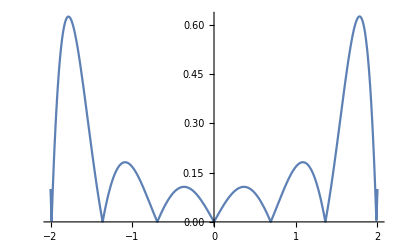

```mathematica
Plot[Abs[Exp[-x]-nwtn[x]],{x,-2,2}]
```

```mathematica
FindMaximum[{Abs[Exp[-x]-nwtn[x]],-2<x<2},{x}]
```

{0.624755,{2→1.78112}}

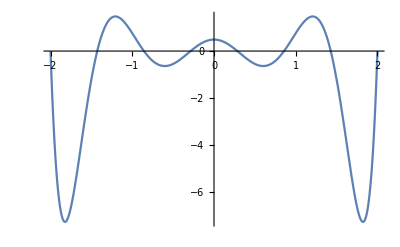

```mathematica
{0.6247548644534717,{2->1.781123465796245}}
Plot[∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{∏_(i=0)^n (x-xdata[i]),-2≤x≤-1},{x}]
```

```mathematica
{1.4749040152533832,{2->-1.2074687411948342}}
ⅇ^2/(8!)×1.4749040152533832
```

{1.4749,{2→-1.20747}}

```mathematica
0.0002702913816777112
```

```mathematica
n1=8
b=2
a=-2
h=(b-a)/n1
XDT={};YDT={};
For[i=0,i≤n1,i++,
xdata1[i]=a+i×h;
ydata1[i]=N[Exp[-xdata1[i]]+0.1*(-1)^(i+2)];
XDT=Append[XDT,xdata1[i]];
YDT=Append[YDT,ydata1[i]];];
Array[xdata1,{n1+1,0}];
Array[ydata1,{n1+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-3/2}, {-1}, {-1/2}, {0}, {1/2}, {1}, {3/2}, {2}}) ({{7.48905609893065}, {4.381689070338065}, {2.818281828459045}, {1.548721270700128}, {1.1}, {0.5065306597126334}, {0.4678794411714423}, {0.12313016014842981}, {0.2353352832366127}})
Array[difftab,{n1+1,n1+1},{0,0}];
For[k=1,k≤n1,k++,
For[i=n1,i≥n1-k,i--,difftab[i,k]=""]];
For[i=0,i≤n1,i++,difftab[i,0]=ydata1[i]];
For [k=1, k≤n1,k++,
For[i=0,i≤n1-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata1[i+k]-xdata1[i])]];
tab1 = Array[difftab,{n+1,n1+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

{-14.9781,-6.57253,-2.81828,-0.774361,0.,0.253265,0.467879,0.184695,0.470671}

7.48906 | -6.21473 |  3.08792 | -1.66682 |  1.18474 | -0.87192 |  0.57133 | -0.32535 |  0.16257
 4.38169 | -3.12681 |  0.58769 |  0.70266 | -0.99505 |  0.84206 | -0.56741 |  0.32491 | 
 2.81828 | -2.53912 |  1.64168 | -1.28745 |  1.11010 | -0.86017 |  0.56979 |  | 
 1.54872 | -0.89744 | -0.28950 |  0.93275 | -1.04032 |  0.84919 |  |  | 
 1.10000 | -1.18694 |  1.10964 | -1.14789 |  1.08265 |  |  |  | 
 0.50653 | -0.07730 | -0.61220 |  1.01740 |  |  |  |  | 
 0.46788 | -0.68950 |  0.91391 |  |  |  |  |  | 
 0.12313 |  0.22441 |  |  |  |  |  |  |

```mathematica
(f^(8)(ξ))/8!=0.16257
ξ=0.16257*8!
```

(f^8 ξ)/8≠0.16257

6554.82

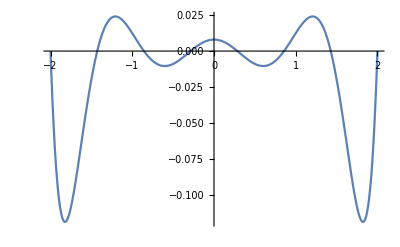

```mathematica
Plot[0.01628*∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{0.16257*∏_(i=0)^n (x-xdata[i]),-2≤x≤2},{x}]
```

```mathematica
{0.2397751457595641,{2->-1.2074689411177095}}
```